# Elastic bodies, plastic impact

## Parameters

```mathematica
param={l1->5.59,l2->5.59,m1->300,m2->300,mb->419725,mO->3000,r->0.12,α->0.5,ρ1->300/5.59,ρ2->300/5.59,EI1->(π/64)*0.24^4*7*10^10,EI2->(π/64)*0.24^4*7*10^10,A1->π 0.12^2,A2->π 0.12^2};
beta={β1->((ω1^2ρ1)/(EI1))^(1/4),β2->((ω2^2ρ2)/(EI2))^(1/4)};
```

```mathematica
θ00=π/2;q10=0;q20=π/2;xb0=4;yb0=2;Q10=0;Q20=0;
```

```mathematica
paramScheme={θ0[t]->θ00,q1[t]->q10,q2[t]->q20,xb[t]->xb0,yb[t]->yb0,Q1[t]->Q10,Q2[t]->Q20};
EulerBernoulli={v1[x1,t]->B1[x1]Q1[t],Derivative[1,0][v1][x1,t]->D[B1[x1],x1]Q1[t],Derivative[0,1][v1][x1,t]->B1[x1]D[Q1[t],t],Derivative[1,1][v1][x1,t]->D[B1[x1],x1]D[Q1[t],t],v2[x2,t]->B2[x2]Q2[t],Derivative[1,0][v2][x2,t]->D[B2[x2],x2]Q2[t],Derivative[0,1][v2][x2,t]->B2[x2]D[Q2[t],t],Derivative[1,1][v2][x2,t]->D[B2[x2],x2]D[Q2[t],t]};
Jxb=1/4 mb r^2;
Jyb=1/4 mb r^2;
Jzb=0;
Jx1=1/3m1 l1^2;
Jx2=1/3 m2 l2^2;
Jb=1/2mb r^2;
J1=1/12m1 l1^2;
J2=1/12m2 l2^2;
Jz=1/2mO r^2;
```

## Kinematics

## Manipulator

We start with a simple manipulator, moving base (that mimics the spacecraft position and orientation) and two rotational links.

```mathematica
Mrotztrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
Mrotztrasl[α,{p1,p2,p3}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | p2
0 | 0 | 1 | p3
0 | 0 | 0 | 1)

```mathematica
elasticMatrix[rx_,ry_,rz_,px_,py_,pz_]:={{1,-rz,ry,px},{rz,1,-rx,py},{-ry,rx,1,pz},{0,0,0,1}};
```

```mathematica
Mfb=Mrotztrasl[0,{xb[t],yb[t],0}];
```

```mathematica
Mb0=Mrotztrasl[θ0[t],{0,0,0}];
```

```mathematica
Mf0=Mfb.Mb0;Mf0//MatrixForm
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | xb[t]
Sin[θ0[t]] | Cos[θ0[t]] | 0 | yb[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M01=Mrotztrasl[q1[t],{l1 Cos[q1[t]],l1 Sin[q1[t]],0}];M01//MatrixForm
```

(Cos[q1[t]] | -Sin[q1[t]] | 0 | l1 Cos[q1[t]]
Sin[q1[t]] | Cos[q1[t]] | 0 | l1 Sin[q1[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

We will write the local deformation along the y-axis as v(x,t)=B(x)T(t)

```mathematica
E01=Mrotztrasl[D[v1[x1,t],x1],{0,v1[x1,t],0}];E01//MatrixForm
```

(Cos[v1^(1,0)[x1,t]] | -Sin[v1^(1,0)[x1,t]] | 0 | 0
Sin[v1^(1,0)[x1,t]] | Cos[v1^(1,0)[x1,t]] | 0 | v1[x1,t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(*E01=elasticMatrix[0,0,0,0,v1[x1,t],0];E01//MatrixForm*)
```

```mathematica
T01=M01.E01;T01//MatrixForm
```

(Cos[q1[t]] Cos[v1^(1,0)[x1,t]]-Sin[q1[t]] Sin[v1^(1,0)[x1,t]] | -Cos[v1^(1,0)[x1,t]] Sin[q1[t]]-Cos[q1[t]] Sin[v1^(1,0)[x1,t]] | 0 | l1 Cos[q1[t]]-Sin[q1[t]] v1[x1,t]
Cos[v1^(1,0)[x1,t]] Sin[q1[t]]+Cos[q1[t]] Sin[v1^(1,0)[x1,t]] | Cos[q1[t]] Cos[v1^(1,0)[x1,t]]-Sin[q1[t]] Sin[v1^(1,0)[x1,t]] | 0 | l1 Sin[q1[t]]+Cos[q1[t]] v1[x1,t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M12=Mrotztrasl[q2[t],{l2 Cos[q2[t]],l2 Sin[q2[t]],0}];M12//MatrixForm
```

(Cos[q2[t]] | -Sin[q2[t]] | 0 | l2 Cos[q2[t]]
Sin[q2[t]] | Cos[q2[t]] | 0 | l2 Sin[q2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
E12=Mrotztrasl[D[v2[x2,t],x2],{0,v2[x2,t],0}];E12//MatrixForm
```

(Cos[v2^(1,0)[x2,t]] | -Sin[v2^(1,0)[x2,t]] | 0 | 0
Sin[v2^(1,0)[x2,t]] | Cos[v2^(1,0)[x2,t]] | 0 | v2[x2,t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(*E12=elasticMatrix[0,0,0,0,v2[x2,t],0];*)
```

```mathematica
T12=Simplify[M12.E12];
```

```mathematica
T02=Simplify[T01.T12];
```

```mathematica
Mf1=Simplify[Mf0.M01];
```

```mathematica
Mf2=Simplify[Mf1.M12];
```

```mathematica
Tf1=Simplify[Mf0.T01];
```

```mathematica
Tf2=Simplify[Tf1.T12];
```

### Origin points

```mathematica
origin={0,0,0,1};
```

```mathematica
Ob=Mfb.origin;Ob//MatrixForm
```

(xb[t]
yb[t]
0
1)

```mathematica
O1=Tf1.origin;
```

```mathematica
EE=Simplify[Tf2.origin];
```

Jacobian matrix:

```mathematica
EE
```

{l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]]-Sin[q1[t]+θ0[t]] v1[x1,t]-Sin[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]] v2[x2,t]+xb[t],l1 Sin[q1[t]+θ0[t]]+l2 Sin[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]]+Cos[q1[t]+θ0[t]] v1[x1,t]+Cos[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]] v2[x2,t]+yb[t],0,1}

## Object

-Graphics-

Let’s consider a circula spinning satellite. In 2D, we have 3 DoF: xb, yOb, and rotation around z.
Coordinats refered to the COM:

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

The jacobian describe the relationship between the velocityOb of the dof and the contact point:

```mathematica
MfO0=Mrotztrasl[0,{xO[t],yO[t],0}];MfO0//MatrixForm
```

(1 | 0 | 0 | xO[t]
0 | 1 | 0 | yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO0O1=Mrotztrasl[Ω[t],{0,0,0}];MO0O1//MatrixForm
```

(Cos[Ω[t]] | -Sin[Ω[t]] | 0 | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO1O2=Mrotztrasl[α,{r Cos[α] ,r Sin[α],0}];MO1O2//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | r Cos[α]
Sin[α] | Cos[α] | 0 | r Sin[α]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MfO1=MfO0.MO0O1;
MfO2=Simplify[MfO0.MO0O1.MO1O2];MfO2//MatrixForm
```

(Cos[α+Ω[t]] | -Sin[α+Ω[t]] | 0 | r Cos[α+Ω[t]]+xO[t]
Sin[α+Ω[t]] | Cos[α+Ω[t]] | 0 | r Sin[α+Ω[t]]+yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
contactP=(MfO2.{0,0,0,1})[[1;;2]];contactP//MatrixForm
velContactP=D[contactP,t];velContactP//MatrixForm
```

(r Cos[α+Ω[t]]+xO[t]
r Sin[α+Ω[t]]+yO[t])

(xO'[t]-r Sin[α+Ω[t]] Ω'[t]
yO'[t]+r Cos[α+Ω[t]] Ω'[t])

```mathematica
Jo=D[contactP,{{xO[t],yO[t],Ω[t]}}];Jo//MatrixForm
```

(1 | 0 | -r Sin[α+Ω[t]]
0 | 1 | r Cos[α+Ω[t]])

```mathematica
Transpose[Jo]//MatrixForm
```

(1 | 0
0 | 1
-r Sin[α+Ω[t]] | r Cos[α+Ω[t]])

```mathematica
Jo.ψ'==velContactP//Simplify
```

True

## Beam Theory

## Link 1

```mathematica
ML1=m2+mO;
JL1=J2+Jz+mO l2^2;
```

```mathematica
B1[x_]:=C1( Cos[β1 x]- Cosh[β1 x]+ν1(Sin[β1 x]-Sinh[β1 x]));
```

```mathematica
freqEq1=(1+Cos[β1 l1]Cosh[β1 l1])-(ML1 β1/(ρ1 A1 l1))(Sin[β1 l1]Cosh[β1 l1]-Cos[β1 l1]Sinh[β1 l1])-(JL1 β1^3/(ρ1 A1 l1^3))(Sin[β1 l1]Cosh[β1 l1]+Cos[β1 l1]Sinh[β1 l1])+(ML1 JL1 β1^4/(ρ1^2 A1^2 l1^4))(1-Cos[β1 l1]Cosh[β1 l1]);
```

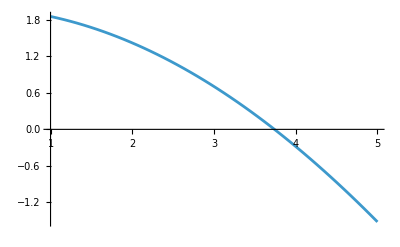

```mathematica
Plot[(freqEq1/.beta/.param),{ω1,1,5}]
```

```mathematica
freq1=FindRoot[(freqEq1/.beta/.param),{ω1,1,5}][[1,2]]
```

3.73983

```mathematica
const1=Simplify[Solve[Integrate[(A1 ρ1/.param)B1[x]^2,{x,0,l1}]==1,C1]][[2,1,2]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ν1=(Sin[β1 l1]-Sinh[β1 l1]+ML1 β1/(ρ1 l1 A1)(Cos[β1 l1]-Cosh[β1 l1]))/(Cos[β1 l1]+Cosh[β1 l1]-ML1 β1/(ρ1 l1 A1)(Sin[β1 l1]-Sinh[β1 l1]));
```

```mathematica
const1/.beta/.ω1->freq1/.param
```

3.25711

## Link 2

```mathematica
ML2=mO;
JL2=Jz;
```

```mathematica
B2[x_]:=C2( Cos[β2 x]- Cosh[β2 x]+ν2(Sin[β2 x]-Sinh[β2 x]));
```

```mathematica
freqEq2=(1+Cos[β2 l2]Cosh[β2 l2])-(ML2 β2/(ρ2 A2 l2))(Sin[β2 l2]Cosh[β2 l2]-Cos[β2 l2]Sinh[β2 l2])-(JL2 β2^3/(ρ2 A2 l2^3))(Sin[β2 l2]Cosh[β2 l2]+Cos[β2 l2]Sinh[β2 l2])+(ML2 JL2 β2^4/(ρ2^2 A2^2 l2^4))(1-Cos[β2 l2]Cosh[β2 l2]);
```

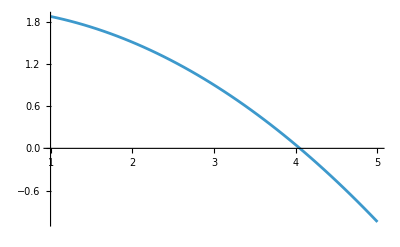

```mathematica
Plot[Simplify[(freqEq2/.beta/.param)],{ω2,1,5}]
```

```mathematica
freq2=FindRoot[(freqEq2/.beta/.param),{ω2,1,5}][[1,2]]
```

4.05048

```mathematica
const2=Simplify[Solve[Integrate[(A2 ρ2/.param)B2[x]^2,{x,0,l2}]==1,C2]][[2,1,2]]//Re;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ν2=(Sin[β2 l2]-Sinh[β2 l2]+ML2 β2/(ρ2 l2 A2)(Cos[β2 l2]-Cosh[β2 l2]))/(Cos[β2 l2]+Cosh[β2 l2]-ML2 β2/(ρ2 l2 A2)(Sin[β2 l2]-Sinh[β2 l2]));
```

```mathematica
const2/.beta/.ω2->freq2/.param
```

3.05637

## Jacobian

```mathematica
EE[[1;;2]]/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param
```

{5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+0.561868 Q1[t] Sin[q1[t]+θ0[t]]+0.559006 Q2[t] Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+xb[t],-0.561868 Cos[q1[t]+θ0[t]] Q1[t]-0.559006 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] Q2[t]+5.59 Sin[q1[t]+θ0[t]]+5.59 Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+yb[t]}

```mathematica
J=FullSimplify[D[EE[[1;;2]]/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param,{{xb[t],yb[t],θ0[t],q1[t],q2[t],Q1[t],Q2[t]}}]];J//MatrixForm
```

(1 | 0 | 0.561868 Cos[q1[t]+θ0[t]] Q1[t]+0.559006 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] Q2[t]-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] | 0.561868 Cos[q1[t]+θ0[t]] Q1[t]+0.559006 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] Q2[t]-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] | 0.559006 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] Q2[t]-5.59 Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] | -0.0860113 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] Q2[t]+0.561868 Sin[q1[t]+θ0[t]]+0.860104 Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] | 0.559006 Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]
0 | 1 | 5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+0.561868 Q1[t] Sin[q1[t]+θ0[t]]+0.559006 Q2[t] Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] | 5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+0.561868 Q1[t] Sin[q1[t]+θ0[t]]+0.559006 Q2[t] Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] | 5.59 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+0.559006 Q2[t] Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] | -0.561868 Cos[q1[t]+θ0[t]]-0.860104 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]-0.0860113 Q2[t] Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] | -0.559006 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]])

## Dynamics

## Manipulator

### IR method

The mass is considered distributed, hence the pseudo inertia tensor can be written like this:

Inertia frame in the com of the round base:

```mathematica
J00={{Jxb,0,0,0},{0,Jyb,0,0},{0,0,Jzb,0},{0,0,0,mb}};J00//MatrixForm
```

((mb r^2)/4 | 0 | 0 | 0
0 | (mb r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mb)

```mathematica
J0f=Simplify[Mf0.J00.Transpose[Mf0]];J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
J11={{Jx1,0,0,-l1/2 m1},{0,0,0,0},{0,0,0,0},{-l1/2 m1,0,0,m1}};J11//MatrixForm
```

((l1^2 m1)/3 | 0 | 0 | -(l1 m1)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l1 m1)/2 | 0 | 0 | m1)

```mathematica
J1f=Simplify[Tf1.J11.Transpose[Tf1]];
```

```mathematica
J22={{Jx2,0,0,-l2/2 m2},{0,0,0,0},{0,0,0,0},{-l2/2 m2,0,0,m2}};J22//MatrixForm
```

((l2^2 m2)/3 | 0 | 0 | -(l2 m2)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l2 m2)/2 | 0 | 0 | m2)

```mathematica
J2f=Simplify[Tf2.J22.Transpose[Tf2]];
```

```mathematica
Wf0=Simplify[D[Mf0,t].Inverse[Mf0]];Wf0//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb=Simplify[D[Mfb,t].Inverse[Mfb]];Wfb//MatrixForm
```

(0 | 0 | 0 | xb'[t]
0 | 0 | 0 | yb'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0=Simplify[D[Mb0,t].Inverse[Mb0]];Wb0//MatrixForm
```

(0 | -θ0'[t] | 0 | 0
θ0'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0Ff=Simplify[Mfb.Wb0.Inverse[Mfb]];Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | yb[t] θ0'[t]
θ0'[t] | 0 | 0 | -xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb+Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Lfbx=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Lfby=({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Lb0=Wb0/θ0'[t];
```

```mathematica
Lb0Ff=Simplify[Mf0.Lb0.Inverse[Mf0]];Lb0Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WT01=FullSimplify[D[T01,t].Inverse[T01]];WT01//MatrixForm
```

(0 | -q1'[t]-v1^(1,1)[x1,t] | 0 | -Sin[q1[t]] v1^(0,1)[x1,t]+(l1 Sin[q1[t]]+Cos[q1[t]] v1[x1,t]) v1^(1,1)[x1,t]
q1'[t]+v1^(1,1)[x1,t] | 0 | 0 | Cos[q1[t]] v1^(0,1)[x1,t]+(-l1 Cos[q1[t]]+Sin[q1[t]] v1[x1,t]) v1^(1,1)[x1,t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W01=FullSimplify[D[M01,t].Inverse[M01]];W01//MatrixForm
```

(0 | -q1'[t] | 0 | 0
q1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

The diagonal contributions appear to be non zero. This is because we have assumed the angle so small that the cosine is 1 and the sine is zero. By assuming again T(t)B’(x)≈0, the diagonal becomes zero and the velocity becomes q1’(t)+B1(x)’T1(t)’.
We also want just W01 since we need L01: we suppose that no forces act on the flexible coordinates, so no motion is enable by them.

```mathematica
L01=W01/q1'[t];
```

```mathematica
L01Ff=Simplify[Mf0.L01.Inverse[Mf0]];L01Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WTf1=FullSimplify[D[Tf1,t].Inverse[Tf1]];WTf1//MatrixForm
```

(0 | -q1'[t]-θ0'[t]-v1^(1,1)[x1,t] | 0 | yb[t] q1'[t]+xb'[t]+yb[t] θ0'[t]-Sin[q1[t]+θ0[t]] v1^(0,1)[x1,t]+(l1 Sin[q1[t]+θ0[t]]+Cos[q1[t]+θ0[t]] v1[x1,t]+yb[t]) v1^(1,1)[x1,t]
q1'[t]+θ0'[t]+v1^(1,1)[x1,t] | 0 | 0 | yb'[t]+Cos[q1[t]+θ0[t]] v1^(0,1)[x1,t]+(-l1 Cos[q1[t]+θ0[t]]+Sin[q1[t]+θ0[t]] v1[x1,t]) v1^(1,1)[x1,t]-xb[t] (q1'[t]+θ0'[t]+v1^(1,1)[x1,t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf1=Simplify[D[Mf1,t].Inverse[Mf1]];
```

```mathematica
WT12=FullSimplify[D[T12,t].Inverse[T12]];WT12//MatrixForm
```

(0 | -q2'[t]-v2^(1,1)[x2,t] | 0 | -Sin[q2[t]] v2^(0,1)[x2,t]+(l2 Sin[q2[t]]+Cos[q2[t]] v2[x2,t]) v2^(1,1)[x2,t]
q2'[t]+v2^(1,1)[x2,t] | 0 | 0 | Cos[q2[t]] v2^(0,1)[x2,t]+(-l2 Cos[q2[t]]+Sin[q2[t]] v2[x2,t]) v2^(1,1)[x2,t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W12=Simplify[D[M12,t].Inverse[M12]];
```

```mathematica
L12=W12/q2'[t];
L12Ff=Simplify[Mf1.L12.Inverse[Mf1]];L12Ff//MatrixForm
```

(0 | -1 | 0 | l1 Sin[q1[t]+θ0[t]]+yb[t]
1 | 0 | 0 | -l1 Cos[q1[t]+θ0[t]]-xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WTf2=FullSimplify[D[Tf2,t].Inverse[Tf2]];WTf2//MatrixForm
```

(0 | -q1'[t]-q2'[t]-θ0'[t]-v1^(1,1)[x1,t]-v2^(1,1)[x2,t] | 0 | (l1 Sin[q1[t]+θ0[t]]+Cos[q1[t]+θ0[t]] v1[x1,t]) q2'[t]+xb'[t]-Sin[q1[t]+θ0[t]] v1^(0,1)[x1,t]-Sin[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]] v2^(0,1)[x2,t]+(l1 Sin[q1[t]+θ0[t]]+Cos[q1[t]+θ0[t]] v1[x1,t]) v1^(1,1)[x1,t]+(l1 Sin[q1[t]+θ0[t]]+l2 Sin[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]]+Cos[q1[t]+θ0[t]] v1[x1,t]+Cos[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]] v2[x2,t]) v2^(1,1)[x2,t]+yb[t] (q1'[t]+q2'[t]+θ0'[t]+v1^(1,1)[x1,t]+v2^(1,1)[x2,t])
q1'[t]+q2'[t]+θ0'[t]+v1^(1,1)[x1,t]+v2^(1,1)[x2,t] | 0 | 0 | (-l1 Cos[q1[t]+θ0[t]]+Sin[q1[t]+θ0[t]] v1[x1,t]) q2'[t]+yb'[t]+Cos[q1[t]+θ0[t]] v1^(0,1)[x1,t]+Cos[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]] v2^(0,1)[x2,t]+(-l1 Cos[q1[t]+θ0[t]]+Sin[q1[t]+θ0[t]] v1[x1,t]) v1^(1,1)[x1,t]+(-l1 Cos[q1[t]+θ0[t]]-l2 Cos[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]]+Sin[q1[t]+θ0[t]] v1[x1,t]+Sin[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x1,t]] v2[x2,t]) v2^(1,1)[x2,t]-xb[t] (q1'[t]+q2'[t]+θ0'[t]+v1^(1,1)[x1,t]+v2^(1,1)[x2,t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf2=Simplify[D[Mf2,t].Inverse[Mf2]];
```

```mathematica
K1=Simplify[1/2Tr[Wf0.J0f.Transpose[Wf0]]];
K2=Simplify[1/2Tr[WTf1.J1f.Transpose[WTf1]]];
K3=Simplify[1/2Tr[WTf2.J2f.Transpose[WTf2]]];
```

```mathematica
L=Simplify[(K1+K2+K3)/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param];
```

By neglecting the constraints forces (since they don’t affect the lagrange equation), we get the actions matrices:

```mathematica
actionMatrix[cx_,cy_,cz_,fx_,fy_,fz_]:={{0,-cz,cy,fx},{cz,0,-cx,fy},{-cy,cx,0,fz},{-fx,-fy,-fz,0}};
```

```mathematica
ϕ0b=actionMatrix[0,0,τ1-τ2,Fx,Fy,0];ϕ0b//MatrixForm
```

(0 | -τ1+τ2 | 0 | Fx
τ1-τ2 | 0 | 0 | Fy
0 | 0 | 0 | 0
-Fx | -Fy | 0 | 0)

```mathematica
ϕbf=FullSimplify[Mf0.ϕ0b.Transpose[Mf0]];
```

```mathematica
ϕ11=actionMatrix[0,0,τ2-τ3,0,0,0];ϕ11//MatrixForm
ϕ1f=FullSimplify[Mf1.ϕ11.Transpose[Mf1]];ϕ1f//MatrixForm
```

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ϕ22=actionMatrix[0,0,τ3,0,0,0];
ϕ2f=FullSimplify[Mf2.ϕ22.Transpose[Mf2]];
```

Let’s derivate the non-lagrangian components:

```mathematica
PSS[Mat1_,Mat2_]:=Mat1[[3,2]]*Mat2[[3,2]]+Mat1[[1,3]]*Mat2[[1,3]]+Mat1[[2,1]]*Mat2[[2,1]]+Mat1[[1,4]]*Mat2[[1,4]]+Mat1[[2,4]]*Mat2[[2,4]]+Mat1[[3,4]]*Mat2[[3,4]];
```

```mathematica
f1=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfbx]]
f2=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfby]]
f3=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lb0Ff]]
f4=FullSimplify[PSS[(ϕ1f+ϕ2f),L01Ff]]
f5=Simplify[PSS[(ϕ2f),L12Ff]]
```

Fx Cos[θ0[t]]-Fy Sin[θ0[t]]

Fy Cos[θ0[t]]+Fx Sin[θ0[t]]

τ1

τ2

τ3

```mathematica
eq1=Simplify[D[D[L,xb'[t]],t]-D[L,xb[t]]-f1];
eq2=Simplify[D[D[L,yb'[t]],t]-D[L,yb[t]]-f2];
eq3=Simplify[D[D[L,θ0'[t]],t]-D[L,θ0[t]]-f3];
eq4=Simplify[D[D[L,q1'[t]],t]-D[L,q1[t]]-f4];
eq5=Simplify[D[D[L,q2'[t]],t]-D[L,q2[t]]-f5];
eq6=Simplify[D[D[L,Q1'[t]],t]-D[L,Q1[t]]];
eq7=Simplify[D[D[L,Q2'[t]],t]-D[L,Q2[t]]];
```

```mathematica
{c,A}=Normal@CoefficientArrays[{eq1,eq2,eq3,eq4,eq5,eq6,eq7},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Q1''[t],Q2''[t],Fx,Fy,τ1,τ2,τ3}];
```

```mathematica
M=Chop[Simplify@A[[1;;7,1;;7]]];
u=-A[[1;;7,8;;12]];
```

```mathematica
M/.paramScheme//MatrixForm
```

(420325. | 0 | -2515.5 | -2515.5 | -1.02687×10^-13 | 208.105 | 5.14168×10^-15
0 | 420325. | -838.5 | -838.5 | -838.5 | 129.016 | 41.985
-2515.5 | -838.5 | 18646.1 | 15624.1 | 3124.81 | -1653.78 | -234.474
-2515.5 | -838.5 | 15624.1 | 15624.1 | 3124.81 | -1653.78 | -234.474
-1.02687×10^-13 | -838.5 | 3124.81 | 3124.81 | 3124.81 | -480.798 | -234.474
208.105 | 129.016 | -1653.78 | -1653.78 | -480.798 | 192.393 | 36.0773
5.14168×10^-15 | 41.985 | -234.474 | -234.474 | -234.474 | 36.0773 | 23.4366)

```mathematica
k1=EI1 Integrate[D[B1[x],x,x]^2/.C1->const1/.beta/.ω1->freq1/.param,{x,0,l1/.param}]/.param
k2=EI2 Integrate[D[B2[x],x,x]^2/.C2->const2/.beta/.ω2->freq2/.param,{x,0,l2/.param}]/.param
```

61889.3

61183.2

```mathematica
K=({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, k1, 0}, {0, 0, 0, 0, 0, 0, k2}});
```

```mathematica
Clear[ω1,ω2]
```

### Classic Lagrangian method

```mathematica
Ob2D=(Mfb.{0,0,0,1})[[1;;2]];
O12D=Simplify[(Tf1.{-l1/2,0,0,1})[[1;;2]]];
EE2D=Simplify[(Tf2.{-l2/2,0,0,1})[[1;;2]]];
```

```mathematica
Vb=D[Ob2D,t];
V1=D[O12D,t];
V2=D[EE2D,t];
```

```mathematica
vbsquare=Simplify[Vb[[1]]^2+Vb[[2]]^2];
v1square=Simplify[V1[[1]]^2+V1[[2]]^2];
v2square=Simplify[V2[[1]]^2+V2[[2]]^2];
```

Inertia wrt CoM:

```mathematica
tb=Simplify[1/2mb vbsquare+1/2Jb (θ0'[t])^2];
t1=Simplify[1/2m1 v1square+1/2J1 (θ0'[t]+q1'[t]+Derivative[1,1][v1][x1,t])^2];
t2=Simplify[1/2m2 v2square+1/2J2 (θ0'[t]+q1'[t]+Derivative[1,1][v1][x1,t]+q2'[t]+Derivative[1,1][v2][x2,t])^2];
```

```mathematica
l=Simplify[(tb+t1+t2)/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param];
```

```mathematica
eq1C=Simplify[D[D[l,xb'[t]],t]-D[l,xb[t]]-f1];
eq2C=Simplify[D[D[l,yb'[t]],t]-D[l,yb[t]]-f2];
eq3C=Simplify[D[D[l,θ0'[t]],t]-D[l,θ0[t]]-f3];
eq4C=Simplify[D[D[l,q1'[t]],t]-D[l,q1[t]]-f4];
eq5C=Simplify[D[D[l,q2'[t]],t]-D[l,q2[t]]-f5];
eq6C=Simplify[D[D[l,Q1'[t]],t]-D[l,Q1[t]]];
eq7C=Simplify[D[D[l,Q2'[t]],t]-D[l,Q2[t]]];
```

```mathematica
{cC,AC}=Normal@CoefficientArrays[{eq1C,eq2C,eq3C,eq4C,eq5C,eq6C,eq7C},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Q1''[t],Q2''[t],Fx,Fy,τ1,τ2,τ3}];
```

```mathematica
MC=Chop[Simplify@AC[[1;;7,1;;7]]];
uC=-AC[[1;;7,8;;12]];
```

```mathematica
MC/.paramScheme//MatrixForm
M/.paramScheme//MatrixForm
```

(420325. | 0 | -2515.5 | -2515.5 | -1.02687×10^-13 | 208.105 | 5.14168×10^-15
0 | 420325. | -838.5 | -838.5 | -838.5 | 129.016 | 41.985
-2515.5 | -838.5 | 18646.1 | 15624. | 3124.81 | -1653.78 | -234.474
-2515.5 | -838.5 | 15624. | 15624. | 3124.81 | -1653.78 | -234.474
-1.02687×10^-13 | -838.5 | 3124.81 | 3124.81 | 3124.81 | -480.798 | -234.474
208.105 | 129.016 | -1653.78 | -1653.78 | -480.798 | 192.393 | 36.0773
5.14168×10^-15 | 41.985 | -234.474 | -234.474 | -234.474 | 36.0773 | 23.4366)

(420325. | 0 | -2515.5 | -2515.5 | -1.02687×10^-13 | 208.105 | 5.14168×10^-15
0 | 420325. | -838.5 | -838.5 | -838.5 | 129.016 | 41.985
-2515.5 | -838.5 | 18646.1 | 15624.1 | 3124.81 | -1653.78 | -234.474
-2515.5 | -838.5 | 15624.1 | 15624.1 | 3124.81 | -1653.78 | -234.474
-1.02687×10^-13 | -838.5 | 3124.81 | 3124.81 | 3124.81 | -480.798 | -234.474
208.105 | 129.016 | -1653.78 | -1653.78 | -480.798 | 192.393 | 36.0773
5.14168×10^-15 | 41.985 | -234.474 | -234.474 | -234.474 | 36.0773 | 23.4366)

## Object

### IR method

```mathematica
IxO=1/4 mO r^2;
IyO=1/4 mO r^2;
IzO=0;
```

```mathematica
JO1O1={{IxO,0,0,0},{0,IyO,0,0},{0,0,IzO,0},{0,0,0,mO}};JO1O1//MatrixForm
```

((mO r^2)/4 | 0 | 0 | 0
0 | (mO r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mO)

```mathematica
J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
JOf=Simplify[MfO1.JO1O1.Transpose[MfO1]];JOf//MatrixForm
```

(1/4 mO (r^2+4 xO[t]^2) | mO xO[t] yO[t] | 0 | mO xO[t]
mO xO[t] yO[t] | 1/4 mO (r^2+4 yO[t]^2) | 0 | mO yO[t]
0 | 0 | 0 | 0
mO xO[t] | mO yO[t] | 0 | mO)

```mathematica
WfO1=Simplify[D[MfO1,t].Inverse[MfO1]];WfO1//MatrixForm
```

(0 | -Ω'[t] | 0 | xO'[t]+yO[t] Ω'[t]
Ω'[t] | 0 | 0 | yO'[t]-xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1=Simplify[D[MO0O1,t].Inverse[MO0O1]];WO0O1//MatrixForm
```

(0 | -Ω'[t] | 0 | 0
Ω'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1Ff=FullSimplify[MfO0.WO0O1.Inverse[MfO0]];WO0O1Ff//MatrixForm
```

(0 | -Ω'[t] | 0 | yO[t] Ω'[t]
Ω'[t] | 0 | 0 | -xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LO0O1Ff=Simplify[WO0O1Ff/Ω'[t]];LO0O1Ff//MatrixForm
```

(0 | -1 | 0 | yO[t]
1 | 0 | 0 | -xO[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LfOx=Lfbx;
LfOy=Lfby;
```

```mathematica
ϕO1O1=actionMatrix[0,0,τO,FOx,FOy,0];
ϕO1O1Ff=FullSimplify[MfO1.ϕO1O1.Transpose[MfO1]];
```

```mathematica
f1O=FullSimplify[PSS[ϕO1O1Ff,LfOx]]
f2O=FullSimplify[PSS[ϕO1O1Ff,LfOy]]
f3O=FullSimplify[PSS[ϕO1O1Ff,LO0O1Ff]]
```

FOx Cos[Ω[t]]-FOy Sin[Ω[t]]

FOy Cos[Ω[t]]+FOx Sin[Ω[t]]

τO

```mathematica
TO=Simplify[1/2Tr[WfO1.JOf.Transpose[WfO1]]];
LO=TO;
```

```mathematica
eq1OIR=Simplify[D[D[LO,xO'[t]],t]-D[L,xO[t]]-f1O];
eq2OIR=Simplify[D[D[LO,yO'[t]],t]-D[L,yO[t]]-f2O];
eq3OIR=Simplify[D[D[LO,Ω'[t]],t]-D[L,Ω[t]]-f3O];
```

```mathematica
{co,Ao}=FullSimplify[Normal@CoefficientArrays[{eq1OIR,eq2OIR,eq3OIR},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}]];
Mo=Ao[[1;;3,1;;3]];
uo=-Ao[[1;;3,4;;6]];
```

```mathematica
Mo//MatrixForm
co//MatrixForm
uo//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

### Classic method

```mathematica
T=1/2 mO(ψ'[[1]]^2+ψ'[[2]]^2)+1/2Iz ψ'[[3]]^2;
```

```mathematica
eq1O=Simplify[D[D[T,xO'[t]],t]-D[T,xO[t]]-f1O];
eq2O=Simplify[D[D[T,yO'[t]],t]-D[T,yO[t]]-f2O];
eq3O=Simplify[D[D[T,Ω'[t]],t]-D[T,Ω[t]]-f3O];
```

```mathematica
{co2,Ao2}=Normal@CoefficientArrays[{eq1O,eq2O,eq3O},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}];
Mo2=Ao2[[1;;3,1;;3]];
uo2=-Ao2[[1;;3,4;;6]];
```

```mathematica
Mo2//MatrixForm
co2//MatrixForm
uo2//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | Iz)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

## Impact

## Pre-impact

Following the 2007 paper, we can find the final condition of the manipulator after the impact:

-Graphics-

```mathematica
Jo//MatrixForm
```

(1 | 0 | -r Sin[α+Ω[t]]
0 | 1 | r Cos[α+Ω[t]])

```mathematica
contactCondition=(θ00+q10+q20+π-(α/.param))
```

5.78319

In the 2007 paper, there is an error when calculating the pseudo-inverse. The correct is the following:

```mathematica
pseudoInverseJo=(Transpose[Jo].Inverse[Jo.Transpose[Jo]]/.Ω[t]->contactCondition/.param)//FullSimplify;pseudoInverseJo//MatrixForm
```

(1. | -3.47692×10^-18
-3.47692×10^-18 | 0.985804
2.89743×10^-17 | 0.118297)

```mathematica
G=Simplify[M+Transpose[J].Transpose[pseudoInverseJo].Mo.pseudoInverseJo.J];
```

```mathematica
p={xb[t],yb[t],θ0[t],q1[t],q2[t],Q1[t],Q2[t]};
p'=D[p,t];
```

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

```mathematica
Chop[G/.EulerBernoulli/.param/.paramScheme]//MatrixForm
```

(423325. | 0 | -19285.5 | -19285.5 | 0 | 1893.71 | 0
0 | 423241. | -17137.4 | -17137.4 | -17137.4 | 2636.85 | 1671.9
-19285.5 | -17137.4 | 203501. | 200479. | 94235.9 | -25095.1 | -9345.69
-19285.5 | -17137.4 | 200479. | 200479. | 94235.9 | -25095.1 | -9345.69
0 | -17137.4 | 94235.9 | 94235.9 | 94235.9 | -14499.6 | -9345.69
1893.71 | 2636.85 | -25095.1 | -25095.1 | -14499.6 | 3296.48 | 1437.97
0 | 1671.9 | -9345.69 | -9345.69 | -9345.69 | 1437.97 | 934.568)

```mathematica
Chop@Inverse[G/.EulerBernoulli/.param/.paramScheme]//MatrixForm
Chop[H /.EulerBernoulli/.param/.paramScheme/.initialConditions1]//MatrixForm
```

(2.38251×10^-6 | 0 | 0 | 1.22918×10^-6 | 0 | 7.98867×10^-6 | 0
0 | 2.38081×10^-6 | 0 | 0 | 1.27893×10^-6 | 0 | 8.53013×10^-6
0 | 0 | 0.000330904 | -0.000330904 | 0 | 0 | 0
1.22918×10^-6 | 0 | -0.000330904 | 0.00146743 | 0.000602081 | 0.0112996 | 0
0 | 1.27893×10^-6 | 0 | 0.000602081 | 0.00162576 | 0.00613159 | 0.0128418
7.98867×10^-6 | 0 | 0 | 0.0112996 | 0.00613159 | 0.113289 | 0
0 | 8.53013×10^-6 | 0 | 0 | 0.0128418 | 0 | 0.129473)

ReplaceAll::reps: {initialConditions1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

H/.initialConditions1

```mathematica
Chop[Transpose[J[[1;;2]]/.param/.paramScheme]]//MatrixForm
Chop[Transpose[pseudoInverseJo].Mo.ψ'/.param/.paramScheme/.initialConditions1]//MatrixForm
```

(1 | 0
0 | 1
-5.59 | -5.59
-5.59 | -5.59
0 | -5.59
0.561868 | 0.860104
0 | 0.559006)

ReplaceAll::reps: {initialConditions1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{3000. xO'[t],2957.41 yO'[t]+2.55521 Ω'[t]}/.initialConditions1

```mathematica
H=Simplify[M. p'+Transpose[J].Transpose[pseudoInverseJo].Mo.ψ'];
```

Final values of the general coordinated of the base+manipulator after the impact:

```mathematica
pf'=Chop[Inverse[G/.EulerBernoulli/.param/.paramScheme].(H /.EulerBernoulli/.param/.paramScheme),10^-10];
```

Final values of the satellite after the impact:

```mathematica
ψf'=(pseudoInverseJo.J.pf')/.EulerBernoulli/.param/.paramScheme;
```

```mathematica
Chop[pseudoInverseJo.J/.EulerBernoulli/.param/.paramScheme]//MatrixForm
```

(1. | 0 | -5.59 | -5.59 | 0 | 0.561868 | 0
0 | 0.985804 | -5.51065 | -5.51065 | -5.51065 | 0.847894 | 0.551071
0 | 0.118297 | -0.661278 | -0.661278 | -0.661278 | 0.101747 | 0.0661285)

### Initial conditions

After the capture, we assume that the object is now perfectlyOb attached to the EE, hence the contact point’s variables coincides with the ones of the EE. We also assume that the spinning velocityOb is resetted:

```mathematica
EEi=EE[[1;;2]]/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.paramScheme;
```

Condition for alignment of the object with the EE:

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.12+xO[t],-2.93915×10^-17+yO[t]}

```mathematica
objectPosI=(Solve[{(EEi[[1]]/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.paramScheme)==(contactP/.param/.Ω[t]->contactCondition)[[1]],(EEi[[2]]/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.paramScheme)==(contactP/.param/.Ω[t]->contactCondition)[[2]]},{xO[t],yO[t]}])[[1]]
```

{xO[t]→-1.71,yO[t]→7.59}

Let’s suppose initial zero velocities of the BM system.

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/2,xb[t]→4,yb[t]→2,Q1[t]→0,Q2[t]→0}

```mathematica
initialConditions1={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,Q1'[t]->0,Q2'[t]->0,xO'[t]->0.1,yO'[t]->0,Ω'[t]->0};
initialConditions2={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,Q1'[t]->0,Q2'[t]->0,xO'[t]->0,yO'[t]->-0.1,Ω'[t]->0};
```

```mathematica
pf1'=pf'/.initialConditions1//Chop
pf2'=pf'/.initialConditions2//Chop
```

{0,0,0,-0.000922536,0.0238521,0.149024,0}

{0,0,0,0,-0.0000251622,0,-0.177148}

```mathematica
ψf1'=ψf'/.initialConditions1//Chop
ψf2'=ψf'/.initialConditions2//Chop
```

{0.0888889,0,0}

{0,-0.0974821,-0.0116979}

```mathematica
a=((Jo.ψf')/.initialConditions1/.param/.paramScheme)
```

{0.0888889,4.48033×10^-14}

```mathematica
b=((J/.EulerBernoulli/.paramScheme/.param).(pf'/.initialConditions1/.param/.paramScheme))
```

{0.0888889,4.48131×10^-14}

```mathematica
a-b//Chop
```

{0,0}

## Post-impact

-Graphics-

```mathematica
EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param
```

{5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+0.561868 Q1[t] Sin[q1[t]+θ0[t]]+0.559006 Q2[t] Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+xb[t],-0.561868 Cos[q1[t]+θ0[t]] Q1[t]-0.559006 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] Q2[t]+5.59 Sin[q1[t]+θ0[t]]+5.59 Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+yb[t]}

```mathematica
EEp=EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param
```

{5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+0.561868 Q1[t] Sin[q1[t]+θ0[t]]+0.559006 Q2[t] Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+xb[t],-0.561868 Cos[q1[t]+θ0[t]] Q1[t]-0.559006 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] Q2[t]+5.59 Sin[q1[t]+θ0[t]]+5.59 Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]+yb[t]}

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.12+xO[t],-2.93915×10^-17+yO[t]}

```mathematica
contactConditionP=(θ0[t]+q1[t]+q2[t]+π-(α/.param));
```

```mathematica
objectPosP=(Solve[{(EE[[1]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param)==(contactP/.param/.Ω[t]->contactConditionP)[[1]],(EE[[2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param)==(contactP/.param/.Ω[t]->contactConditionP)[[2]]},{xO[t],yO[t]}])[[1]];
```

```mathematica
ψp={objectPosP[[1,2]],objectPosP[[2,2]],contactConditionP};
```

We can now write the Jacobian matrix of the object as a function of the EE:

```mathematica
EEsubst={ψ[[1]]->ψp[[1]],ψ[[2]]->ψp[[2]],ψ[[3]]->ψp[[3]]}
```

{xO[t]→-1. (-5.59 Cos[q1[t]+θ0[t]]+0.12 Cos[3.14159+q1[t]+q2[t]+θ0[t]]-5.59 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]-0.561868 Q1[t] Sin[q1[t]+θ0[t]]-0.559006 Q2[t] Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]-xb[t]),yO[t]→-1. (0.561868 Cos[q1[t]+θ0[t]] Q1[t]+0.559006 Cos[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]] Q2[t]-5.59 Sin[q1[t]+θ0[t]]+0.12 Sin[3.14159+q1[t]+q2[t]+θ0[t]]-5.59 Sin[q1[t]-0.153865 Q1[t]+q2[t]+θ0[t]]-yb[t]),Ω[t]→2.64159+q1[t]+q2[t]+θ0[t]}

```mathematica
Jop=Jo/.EEsubst;
```

```mathematica
pseudoInverseJop=Transpose[Jop].Inverse[Jop.Transpose[Jop]]//Simplify;
```

```mathematica
Mp=M+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.J;
```

```mathematica
Cp=c+Transpose[J].Transpose[pseudoInverseJop].Mo.D[pseudoInverseJop,t].J.p'+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.D[J,t].p'+Transpose[J].Transpose[pseudoInverseJop].co;
```

```mathematica
eqMotion=Mp.D[p,t,t]+Cp+K.p;
```

```mathematica
Dimensions[eqMotion]
```

{7}

### Fundamental frequencies around equilibrium point

```mathematica
(Mp/.paramScheme/.param)//MatrixForm
```

(423325. | -2.06394×10^-14 | -19285.5 | -19285.5 | -2.32526×10^-12 | 1893.71 | 2.20296×10^-13
-2.06394×10^-14 | 423241. | -17137.4 | -17137.4 | -17137.4 | 2636.85 | 1671.9
-19285.5 | -17137.4 | 203501.+0. ⅈ | 200479.+0. ⅈ | 94235.9+0. ⅈ | -25095.1 | -9345.69
-19285.5 | -17137.4 | 200479.+0. ⅈ | 200479.+0. ⅈ | 94235.9+0. ⅈ | -25095.1 | -9345.69
-2.21158×10^-12 | -17137.4 | 94235.9+0. ⅈ | 94235.9+0. ⅈ | 94235.9 | -14499.6 | -9345.69
1893.71 | 2636.85 | -25095.1+0. ⅈ | -25095.1+0. ⅈ | -14499.6 | 3296.48+0. ⅈ | 1437.97+0. ⅈ
2.27401×10^-13 | 1671.9 | -9345.69+0. ⅈ | -9345.69+0. ⅈ | -9345.69 | 1437.97 | 934.568)

```mathematica
K//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 61889.3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 61183.2)

```mathematica
Solve[Det[K-ω^2(Mp/.paramScheme/.param)]==0,ω]
```

{{ω→-89.0032},{ω→-83.7339},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→83.7339},{ω→89.0032}}

```mathematica
paramSchemeParallel={θ0[t]->π/2,q1[t]->160,q2[t]->0,xb[t]->4,yb[t]->2,Q1[t]->0,Q2[t]->0};
```

```mathematica
omega1=Solve[Det[K-ω^2(Mp/.paramScheme/.param)]==0,ω][[14,1,2]]
omega2=Solve[Det[K-ω^2(Mp/.paramScheme/.param)]==0,ω][[13,1,2]]
```

89.0032

83.7339

```mathematica
Solve[Det[K-ω^2(Mp/.paramSchemeParallel/.param)]==0,ω][[14,1,2]]
Solve[Det[K-ω^2(Mp/.paramSchemeParallel/.param)]==0,ω][[13,1,2]]
```

143.343

84.4019

```mathematica
P1=1/(omega1/(2π))
P2=1/(omega2/(2π))
```

0.070595

0.0750375

```mathematica
Knew=({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 2799, 0}, {0, 0, 0, 0, 0, 0, 100}});
```

```mathematica
Solve[Det[Knew-ω^2(Mp/.paramScheme/.param)]==0,ω]
```

{{ω→-17.8072},{ω→-3.59824},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→0},{ω→3.59824},{ω→17.8072}}

```mathematica
omega1new=Solve[Det[Knew-ω^2(Mp/.paramScheme/.param)]==0,ω][[14,1,2]]
omega2new=Solve[Det[Knew-ω^2(Mp/.paramScheme/.param)]==0,ω][[13,1,2]]
```

17.8072

3.59824

### Simulation with no control

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/2,xb[t]→4,yb[t]→2,Q1[t]→0,Q2[t]→0}

```mathematica
NDinitialCondition1={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,Q1[0]==Q10,Q2[0]==Q20,xb'[0]==pf1'[[1]],yb'[0]==pf1'[[2]],θ0'[0]==pf1'[[3]],q1'[0]==pf1'[[4]],q2'[0]==pf1'[[5]],Q1'[0]==pf1'[[6]],Q2'[0]==pf1'[[7]]};
NDinitialCondition2={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,Q1[0]==Q10,Q2[0]==Q20,xb'[0]==pf2'[[1]],yb'[0]==pf2'[[2]],θ0'[0]==pf2'[[3]],q1'[0]==pf2'[[4]],q2'[0]==pf2'[[5]],Q1'[0]==pf2'[[6]],Q2'[0]==pf2'[[7]]};
```

```mathematica
solMotion1=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,(eqMotion[[6]]/.param)==0,(eqMotion[[7]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t],Q1[t],Q2[t]},{t,0,500},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotion2=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,(eqMotion[[6]]/.param)==0,(eqMotion[[7]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t],Q1[t],Q2[t]},{t,0,500},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[{{0., 500.}}, <>][t],yb[t]→InterpolatingFunction[{{0., 500.}}, <>][t],θ0[t]→InterpolatingFunction[{{0., 500.}}, <>][t],q1[t]→InterpolatingFunction[{{0., 500.}}, <>][t],q2[t]→InterpolatingFunction[{{0., 500.}}, <>][t],Q1[t]→InterpolatingFunction[{{0., 500.}}, <>][t],Q2[t]→InterpolatingFunction[{{0., 500.}}, <>][t]}

{xb[t]→InterpolatingFunction[{{0., 500.}}, <>][t],yb[t]→InterpolatingFunction[{{0., 500.}}, <>][t],θ0[t]→InterpolatingFunction[{{0., 500.}}, <>][t],q1[t]→InterpolatingFunction[{{0., 500.}}, <>][t],q2[t]→InterpolatingFunction[{{0., 500.}}, <>][t],Q1[t]→InterpolatingFunction[{{0., 500.}}, <>][t],Q2[t]→InterpolatingFunction[{{0., 500.}}, <>][t]}

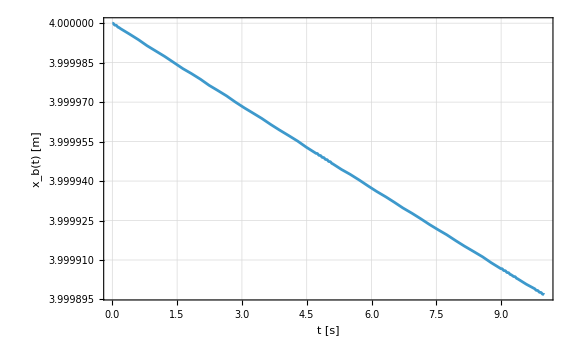
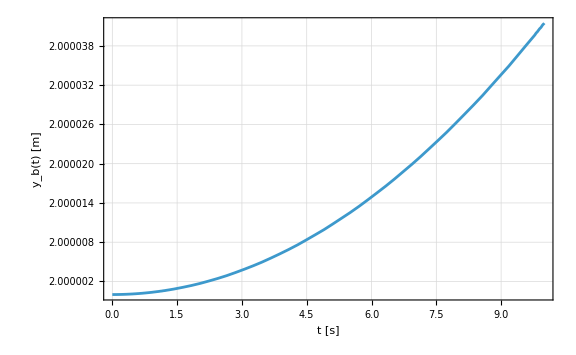
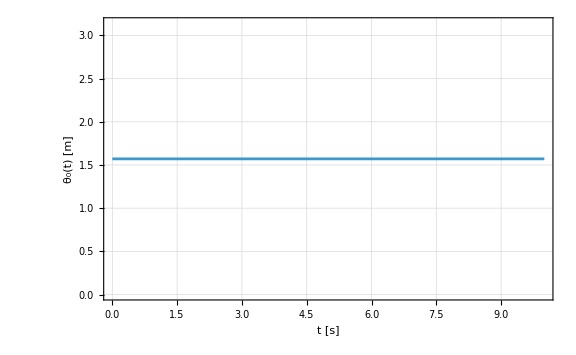
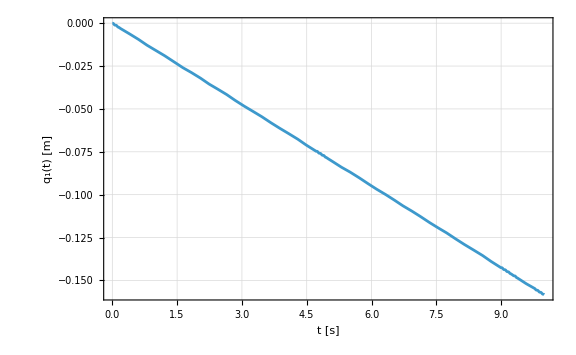
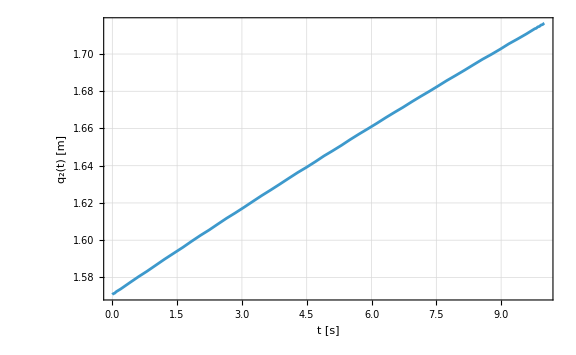
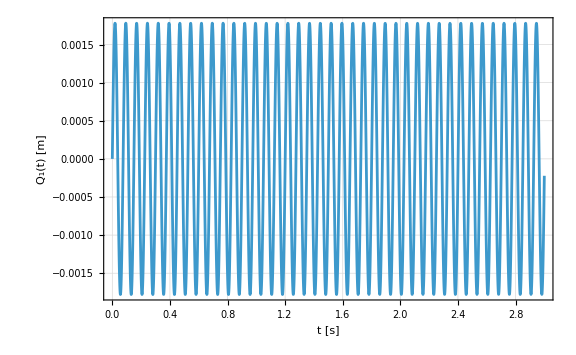
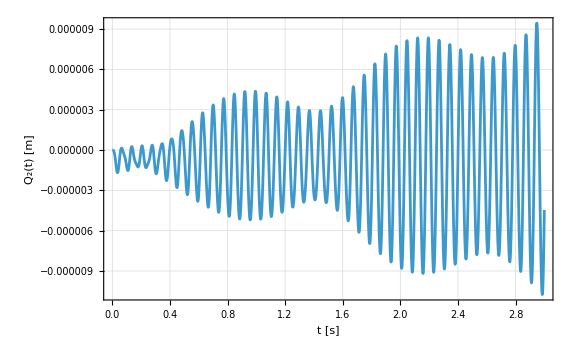

```mathematica
Row[{Plot[solMotion1[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],Plot[solMotion1[[6,2]],{t,0,3},Frame->True,Axes->False,FrameLabel->{"t [s]","Q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],Plot[solMotion1[[7,2]],{t,0,3},Frame->True,Axes->False,FrameLabel->{"t [s]","Q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

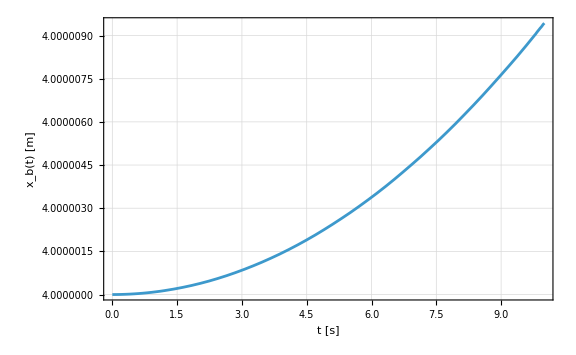
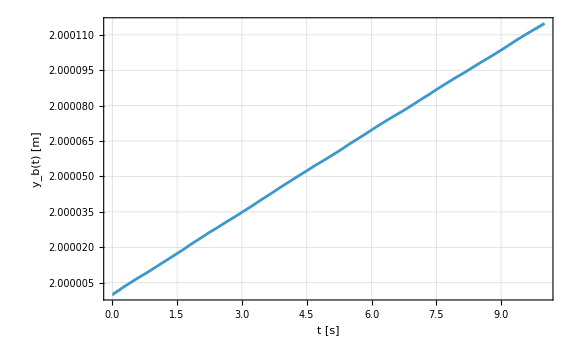
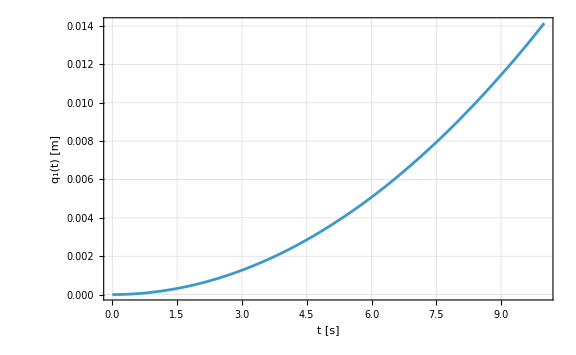
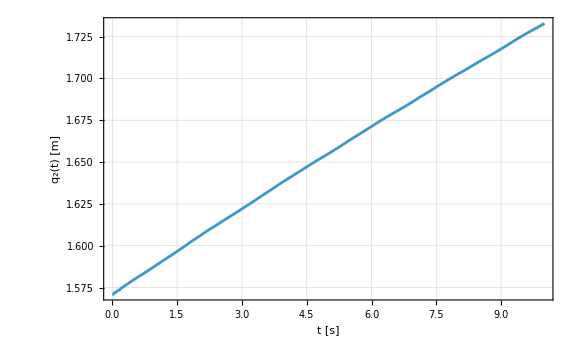
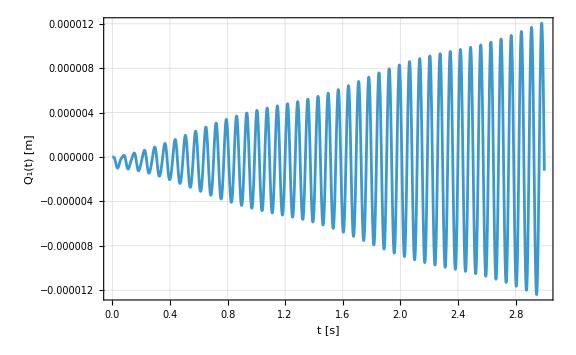
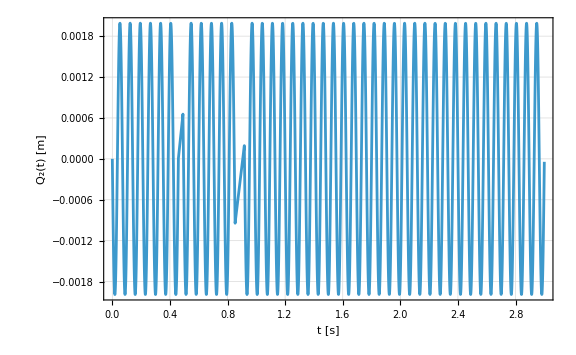
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotion2[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],Plot[solMotion2[[6,2]],{t,0,3},Frame->True,Axes->False,FrameLabel->{"t [s]","Q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],Plot[solMotion2[[7,2]],{t,0,3},Frame->True,Axes->False,FrameLabel->{"t [s]","Q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.paramScheme,O1[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.paramScheme,EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.paramScheme},PlotMarkers->{Automatic, 5}];
```

```mathematica
RobotPlotAfter1=ListLinePlot[{Ob[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->10},PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
RobotPlotAfter2=ListLinePlot[{Ob[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion2/.t->10},PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
```

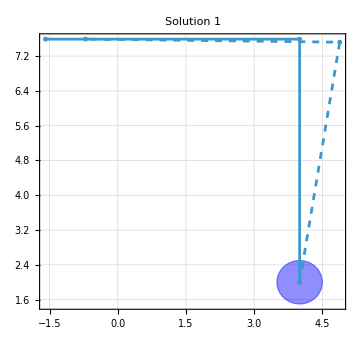
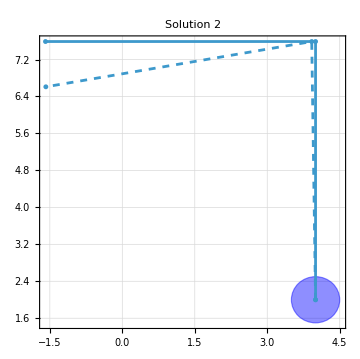

```mathematica
Row[{Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->10,r]}]],RobotPlot,RobotPlotAfter1},Frame->True,GridLines->Automatic,PlotLabel->"Solution 1",ImageSize->Medium],Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion2/.t->10,r]}]],RobotPlot,RobotPlotAfter2},Frame->True,GridLines->Automatic,PlotLabel->"Solution 2",ImageSize->Medium]}]
```

```mathematica
RobotPlotAfter=ListLinePlot[{Ob[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau,O1[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau,EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau},PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
```

$Aborted

```mathematica
vid1=Manipulate[Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->tau,r]}]],RobotPlot,ListLinePlot[{Ob[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau,O1[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau,EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau},PlotMarkers->{Automatic, 5},PlotStyle->Dashed]},Frame->True,GridLines->Automatic,PlotLabel->"Solution 1",ImageSize->Medium,PlotRange->{{-2,15},{-9,8}}],{tau,0,500}]
vid2=Manipulate[Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->tau,r]}]],RobotPlot,ListLinePlot[{Ob[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau,O1[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion2/.t->tau,EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion2/.t->tau},PlotMarkers->{Automatic, 5},PlotStyle->Dashed]},Frame->True,GridLines->Automatic,PlotLabel->"Solution 1",ImageSize->Medium,PlotRange->{{-2,16},{-10,8}}],{tau,0,500}]
```

```mathematica
(*Export["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/simulation_1.mp4",Manipulate[Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->tau,r]}]],RobotPlot,ListLinePlot[{Ob[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau,O1[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau,EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau},PlotMarkers->{Automatic, 5},PlotStyle->Dashed]},Frame->True,GridLines->Automatic,PlotLabel->"Solution 1",ImageSize->Medium,PlotRange->{{-2,15},{-9,8}}],{tau,0,500},AutorunSequencing->{{0,500}}],"AnimationDuration"->20];*)
(*Export["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/simulation_2.mp4",Manipulate[Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->tau,r]}]],RobotPlot,ListLinePlot[{Ob[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion1/.t->tau,O1[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion2/.t->tau,EE[[1;;2]]/.param/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.{ω1->freq1,ω2->freq2}/.{x1->l1,x2->l2}/.param/.solMotion2/.t->tau},PlotMarkers->{Automatic, 5},PlotStyle->Dashed]},Frame->True,GridLines->Automatic,PlotLabel->"Solution 2",ImageSize->Medium,PlotRange->{{-2,16},{-10,8}}],{tau,0,500},AutorunSequencing->{{0,500}}],"AnimationDuration"->20];*)
```

### Simulation with control

```mathematica
Kp=1IdentityMatrix[3];
Kv=2 Sqrt[Kp];
```

```mathematica
pd={θ0[t],q1[t],q2[t]}/.paramScheme
pd'={0,0,0};
```

{π/2,0,π/2}

```mathematica
pA={xb[t],yb[t],θ0[t],q1[t],q2[t]};
pA'=D[pA,t];
pA3={θ0[t],q1[t],q2[t]};
pA3'=D[pA3,t];
pnc={xb[t],yb[t],Q1[t],Q2[t]};
```

```mathematica
Mtt=Mp[[1;;2,1;;2]]/.param;
Mtr=Mp[[1;;2,3;;5]]/.param;
Mte=Mp[[1;;2,6;;7]]/.param;
Mrt=Mp[[3;;5,1;;2]]/.param;
Mrr=Mp[[3;;5,3;;5]]/.param;
Mre=Mp[[3;;5,6;;7]]/.param;
Met=Mp[[6;;7,1;;2]]/.param;
Mer=Mp[[6;;7,3;;5]]/.param;
Mee=Mp[[6;;7,6;;7]]/.param;
```

```mathematica
Ct=Cp[[1;;2]]/.param;
Cr=Cp[[3;;5]]/.param;
Ce=Cp[[6;;7]]/.param;
```

```mathematica
Kpp=K[[6;;7,6;;7]];
```

```mathematica
Mrnc=ArrayFlatten[{{Mrt,Mre}}];
Mncr=ArrayFlatten[{{Mtr},{Mer}}];
Mnc=ArrayFlatten[{{Mtt,Mte},{Met,Mee}}];
Cnc=Join[Ct,Ce];
```

```mathematica
Khat=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, Kpp[[1,1]], 0}, {0, 0, 0, Kpp[[2,2]]}});
```

```mathematica
Mhat=Mrr-Mrnc.Inverse[Mnc].Mncr;
Chat=Cr-Mrnc.Inverse[Mnc].Cnc-Mrnc.Inverse[Mnc].Khat.pnc;
```

```mathematica
U=-Mhat.(Kv.(pA3'-pd')+Kp.(pA3-pd))+Chat;
```

Let’s suppose that the oscillation is the same as in the uncontrolled behaviour:

```mathematica
eqMotionControl1=Mp[[1,1;;7]].D[p,t,t]+Cp[[1]];
eqMotionControl2=Mp[[2,1;;7]].D[p,t,t]+Cp[[2]];
eqMotionControl3=Mp[[3,1;;7]].D[p,t,t]+Cp[[3]]-U[[1]];
eqMotionControl4=Mp[[4,1;;7]].D[p,t,t]+Cp[[4]]-U[[2]];
eqMotionControl5=Mp[[5,1;;7]].D[p,t,t]+Cp[[5]]-U[[3]];
eqMotionControl6=Mp[[6,1;;7]].D[p,t,t]+Cp[[6]]+K[[6,All]].p;
eqMotionControl7=Mp[[7,1;;7]].D[p,t,t]+Cp[[7]]+K[[7,All]].p;
```

```mathematica
solMotionControl1=Monitor[NDSolve[{(eqMotionControl1/.param)==0,(eqMotionControl2/.param)==0,(eqMotionControl3/.param)==0,(eqMotionControl4/.param)==0,(eqMotionControl5/.param)==0,(eqMotionControl6/.param)==0,(eqMotionControl7/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t],Q1[t],Q2[t]},{t,0,10},Method->{"EquationSimplification"->"Residual"},EvaluationMonitor:>(monitor=Row[{"t = ",CForm[t]}])],monitor]
solMotionControl2=Monitor[NDSolve[{(eqMotionControl1/.param)==0,(eqMotionControl2/.param)==0,(eqMotionControl3/.param)==0,(eqMotionControl4/.param)==0,(eqMotionControl5/.param)==0,(eqMotionControl6/.param)==0,(eqMotionControl7/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t],Q1[t],Q2[t]},{t,0,10},Method->{"EquationSimplification"->"Residual"},EvaluationMonitor:>(monitor=Row[{"t = ",CForm[t]}])],monitor]
```

{{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t],Q1[t]→InterpolatingFunction[…][t],Q2[t]→InterpolatingFunction[…][t]}}

{{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t],Q1[t]→InterpolatingFunction[…][t],Q2[t]→InterpolatingFunction[…][t]}}

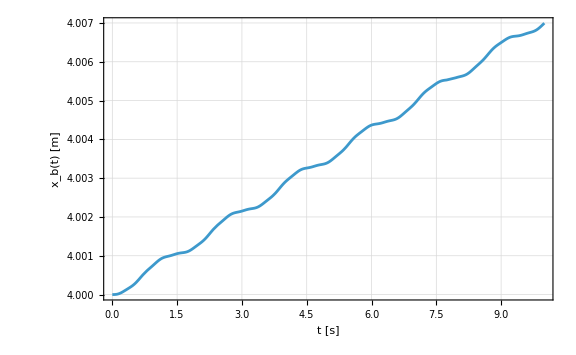
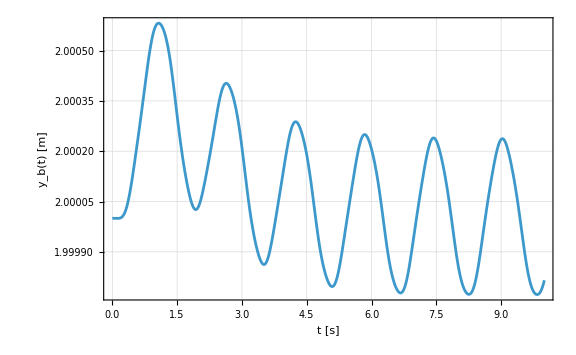
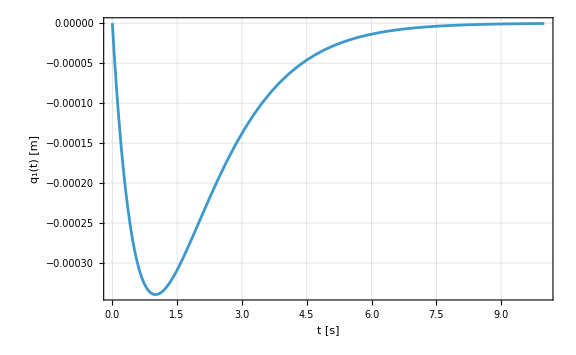
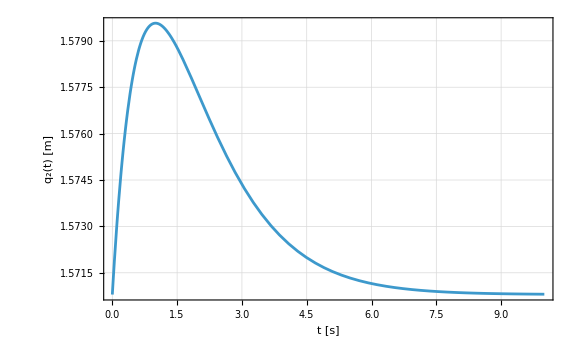
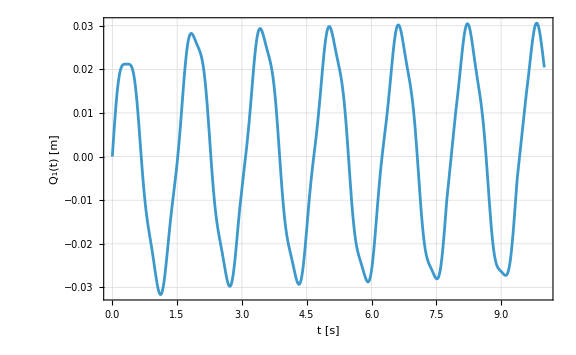
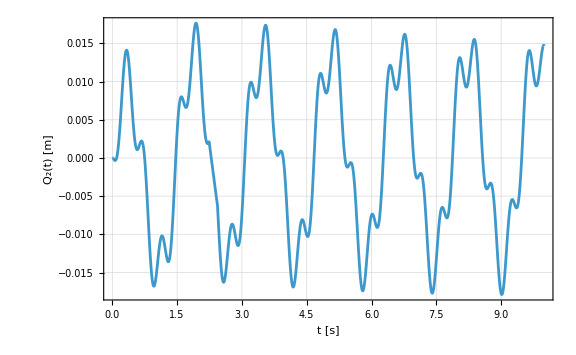
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotionControl1[[1,1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[1,2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[1,3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[1,4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[1,5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],Plot[solMotionControl1[[1,6,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","Q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],Plot[solMotionControl1[[1,7,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","Q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

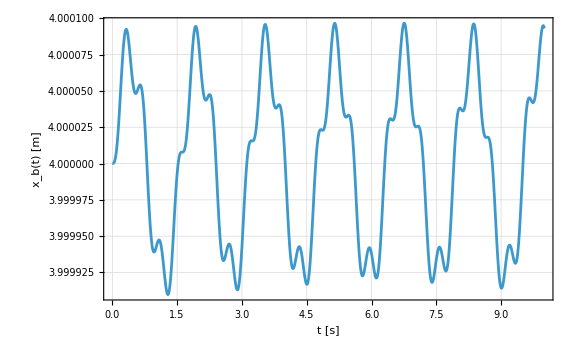
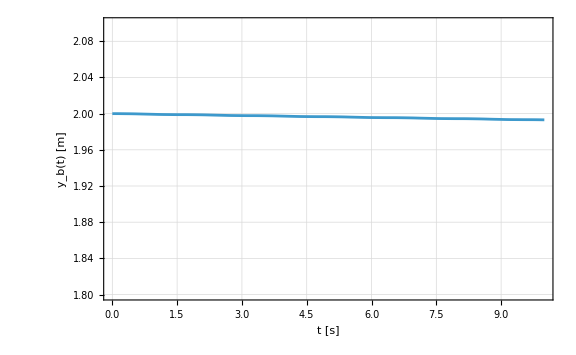
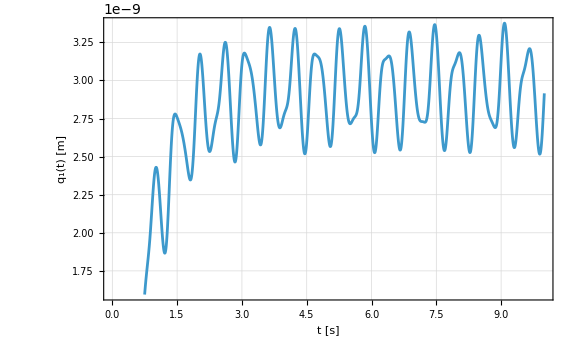
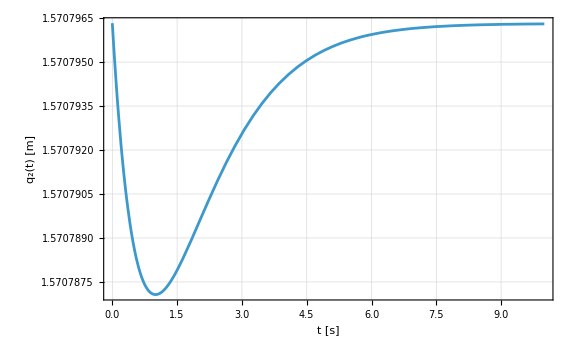
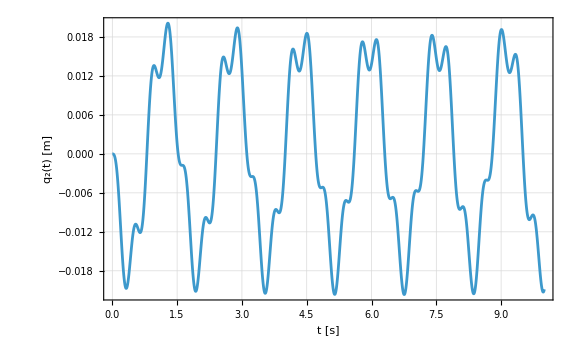
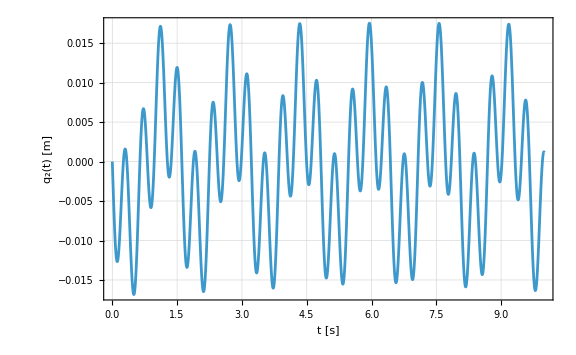
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotionControl2[[1,1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[1,2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.8,2.1}}],
Plot[solMotionControl2[[1,3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[1,4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[1,5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],Plot[solMotionControl2[[1,6,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],Plot[solMotionControl2[[1,7,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```